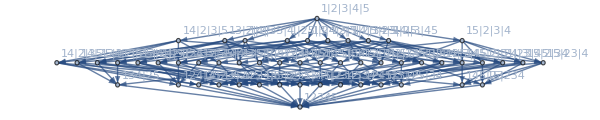

```mathematica
g=Graph[MobiusGraphSimple[K5Key,allGraphs5]]
```

```mathematica
VertexList[g]
```

{n12x34x5,n12x35x4,n12x3x45,n13x24x5,n13x25x4,n13x2x45,n14x23x5,n14x25x3,n14x2x35,n15x23x4,n15x24x3,n15x2x34,n1x23x45,n1x24x35,n1x25x34,n1x2x3x4x5,n12345,n1234x5,n1235x4,n123x45,n123x4x5,n1245x3,n124x35,n124x3x5,n125x34,n125x3x4,n12x345,n12x3x4x5,n1345x2,n134x25,n134x2x5,n135x24,n135x2x4,n13x245,n13x2x4x5,n145x23,n145x2x3,n14x235,n14x2x3x5,n15x234,n15x2x3x4,n1x2345,n1x234x5,n1x235x4,n1x23x4x5,n1x245x3,n1x24x3x5,n1x25x3x4,n1x2x345,n1x2x34x5,n1x2x35x4,n1x2x3x45}

```mathematica
Descendents[g,{n1x2x34}]
```

{}

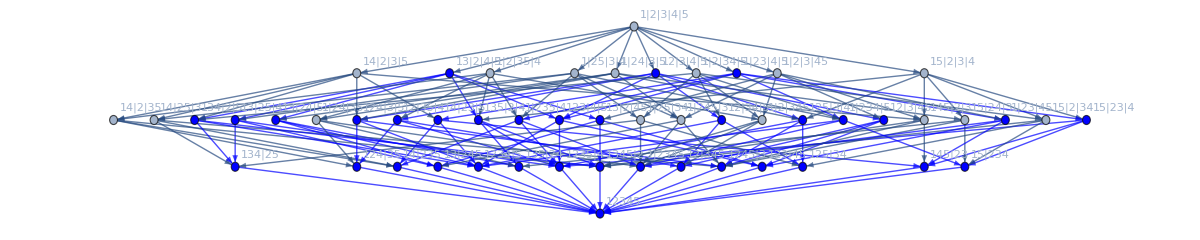

```mathematica
With[{edges=Descendents[g,{n12x3x4x5,n13x2x4x5,n1x23x4x5}]},
Graph[g,
EdgeStyle->Table[e->Blue,{e,edges}],
VertexStyle->Table[v->Blue,{v,DeleteDuplicates[Flatten[Table[{e[[1]],e[[2]]},{e,edges}]]]}],
ImageSize->1200
]]
```

```mathematica
PartitionIntersect[vertices_]:=Block[{edges=Descendents[g,vertices], vertic,counts},
vertic=DeleteDuplicates[Flatten[Table[{e[[1]],e[[2]]},{e,edges}]]];
counts=Table[StringCount[SymbolName[v],"x"],{v,vertic}];
Map[Last,Sort[Tally[counts],#1>#2&]]
]
```

```mathematica
PartitionIntersect[{n12x3x4x5,n13x2x4x5,n1x23x4x5}]
```

{3,16,15,1}

```mathematica
DoubleVertices=Select[VertexList[g],StringCount[SymbolName[#],"x"]==3&]
```

{n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n1x2x34x5,n1x2x35x4,n1x2x3x45}

```mathematica
TableForm[
Table[PartitionIntersect[{v1,v2,v3}],{v1,DoubleVertices},{v2,DoubleVertices},{v3,{First[DoubleVertices]}}],
TableDepth->3]
```

{1,6,7,1} | {2,11,11,1} | {2,11,11,1} | {2,11,11,1} | {2,11,11,1} | {2,11,11,1} | {2,11,11,1} | {2,11,11,1} | {2,11,11,1} | {2,11,11,1}
{2,11,11,1} | {2,11,11,1} | {3,15,13,1} | {3,15,13,1} | {3,16,15,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1}
{2,11,11,1} | {3,15,13,1} | {2,11,11,1} | {3,15,13,1} | {3,15,13,1} | {3,16,15,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1}
{2,11,11,1} | {3,15,13,1} | {3,15,13,1} | {2,11,11,1} | {3,15,13,1} | {3,15,13,1} | {3,16,15,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1}
{2,11,11,1} | {3,16,15,1} | {3,15,13,1} | {3,15,13,1} | {2,11,11,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1}
{2,11,11,1} | {3,15,13,1} | {3,16,15,1} | {3,15,13,1} | {3,15,13,1} | {2,11,11,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1}
{2,11,11,1} | {3,15,13,1} | {3,15,13,1} | {3,16,15,1} | {3,15,13,1} | {3,15,13,1} | {2,11,11,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1}
{2,11,11,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {2,11,11,1} | {3,15,13,1} | {3,15,13,1}
{2,11,11,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {2,11,11,1} | {3,15,13,1}
{2,11,11,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {3,15,13,1} | {2,11,11,1}

```mathematica
Tally[Flatten[Table[If[v1≠v2&&v2≠v3&&v3≠v1,PartitionIntersect[{v1,v2,v3}],{}],{v1,DoubleVertices},{v2,Select[DoubleVertices,#≠v1&]},{v3,Select[DoubleVertices,#≠v1&&#!=v2&]}],2]]
```

{}

```mathematica
Tally[Flatten[
Table[
Table[
Table[
Table[
PartitionIntersect[{v0,v1,v2,v3}],
{v0,Select[DoubleVertices,ToString[#]≠ToString[v3]&&ToString[#]≠ToString[v2]&&ToString[#]≠ToString[v1]&]}
],
{v1,Select[DoubleVertices,ToString[#]≠ToString[v3]&&ToString[#]≠ToString[v2]&]}
],
{v2,Select[DoubleVertices,ToString[#]≠ToString[v3]&]}
],
{v3,DoubleVertices}
],3]]
```

{{{4,18,14,1},3000},{{4,19,15,1},1680},{{4,18,13,1},360}}

```mathematica
Length[Subsets[DoubleVertices]]
```

1024

```mathematica
Select[
Flatten[
Table[
Table[
Table[
{PartitionIntersect[{v1,v2,v3}],{v1,v2,v3}},
{v1,Select[DoubleVertices,ToString[#]≠ToString[v3]&&ToString[#]≠ToString[v2]&]}
],
{v2,Select[DoubleVertices,ToString[#]≠ToString[v3]&]}
],
{v3,DoubleVertices}
],
2],
#[[1]]=={3,16,15,1}&]
```

{{{3,16,15,1},{n1x23x4x5,n13x2x4x5,n12x3x4x5}},{{3,16,15,1},{n1x24x3x5,n14x2x3x5,n12x3x4x5}},{{3,16,15,1},{n1x25x3x4,n15x2x3x4,n12x3x4x5}},{{3,16,15,1},{n13x2x4x5,n1x23x4x5,n12x3x4x5}},{{3,16,15,1},{n14x2x3x5,n1x24x3x5,n12x3x4x5}},{{3,16,15,1},{n15x2x3x4,n1x25x3x4,n12x3x4x5}},{{3,16,15,1},{n1x23x4x5,n12x3x4x5,n13x2x4x5}},{{3,16,15,1},{n1x2x34x5,n14x2x3x5,n13x2x4x5}},{{3,16,15,1},{n1x2x35x4,n15x2x3x4,n13x2x4x5}},{{3,16,15,1},{n12x3x4x5,n1x23x4x5,n13x2x4x5}},{{3,16,15,1},{n14x2x3x5,n1x2x34x5,n13x2x4x5}},{{3,16,15,1},{n15x2x3x4,n1x2x35x4,n13x2x4x5}},{{3,16,15,1},{n1x24x3x5,n12x3x4x5,n14x2x3x5}},{{3,16,15,1},{n1x2x34x5,n13x2x4x5,n14x2x3x5}},{{3,16,15,1},{n1x2x3x45,n15x2x3x4,n14x2x3x5}},{{3,16,15,1},{n12x3x4x5,n1x24x3x5,n14x2x3x5}},{{3,16,15,1},{n13x2x4x5,n1x2x34x5,n14x2x3x5}},{{3,16,15,1},{n15x2x3x4,n1x2x3x45,n14x2x3x5}},{{3,16,15,1},{n1x25x3x4,n12x3x4x5,n15x2x3x4}},{{3,16,15,1},{n1x2x35x4,n13x2x4x5,n15x2x3x4}},{{3,16,15,1},{n1x2x3x45,n14x2x3x5,n15x2x3x4}},{{3,16,15,1},{n12x3x4x5,n1x25x3x4,n15x2x3x4}},{{3,16,15,1},{n13x2x4x5,n1x2x35x4,n15x2x3x4}},{{3,16,15,1},{n14x2x3x5,n1x2x3x45,n15x2x3x4}},{{3,16,15,1},{n13x2x4x5,n12x3x4x5,n1x23x4x5}},{{3,16,15,1},{n12x3x4x5,n13x2x4x5,n1x23x4x5}},{{3,16,15,1},{n1x2x34x5,n1x24x3x5,n1x23x4x5}},{{3,16,15,1},{n1x2x35x4,n1x25x3x4,n1x23x4x5}},{{3,16,15,1},{n1x24x3x5,n1x2x34x5,n1x23x4x5}},{{3,16,15,1},{n1x25x3x4,n1x2x35x4,n1x23x4x5}},{{3,16,15,1},{n14x2x3x5,n12x3x4x5,n1x24x3x5}},{{3,16,15,1},{n12x3x4x5,n14x2x3x5,n1x24x3x5}},{{3,16,15,1},{n1x2x34x5,n1x23x4x5,n1x24x3x5}},{{3,16,15,1},{n1x2x3x45,n1x25x3x4,n1x24x3x5}},{{3,16,15,1},{n1x23x4x5,n1x2x34x5,n1x24x3x5}},{{3,16,15,1},{n1x25x3x4,n1x2x3x45,n1x24x3x5}},{{3,16,15,1},{n15x2x3x4,n12x3x4x5,n1x25x3x4}},{{3,16,15,1},{n12x3x4x5,n15x2x3x4,n1x25x3x4}},{{3,16,15,1},{n1x2x35x4,n1x23x4x5,n1x25x3x4}},{{3,16,15,1},{n1x2x3x45,n1x24x3x5,n1x25x3x4}},{{3,16,15,1},{n1x23x4x5,n1x2x35x4,n1x25x3x4}},{{3,16,15,1},{n1x24x3x5,n1x2x3x45,n1x25x3x4}},{{3,16,15,1},{n14x2x3x5,n13x2x4x5,n1x2x34x5}},{{3,16,15,1},{n13x2x4x5,n14x2x3x5,n1x2x34x5}},{{3,16,15,1},{n1x24x3x5,n1x23x4x5,n1x2x34x5}},{{3,16,15,1},{n1x23x4x5,n1x24x3x5,n1x2x34x5}},{{3,16,15,1},{n1x2x3x45,n1x2x35x4,n1x2x34x5}},{{3,16,15,1},{n1x2x35x4,n1x2x3x45,n1x2x34x5}},{{3,16,15,1},{n15x2x3x4,n13x2x4x5,n1x2x35x4}},{{3,16,15,1},{n13x2x4x5,n15x2x3x4,n1x2x35x4}},{{3,16,15,1},{n1x25x3x4,n1x23x4x5,n1x2x35x4}},{{3,16,15,1},{n1x23x4x5,n1x25x3x4,n1x2x35x4}},{{3,16,15,1},{n1x2x3x45,n1x2x34x5,n1x2x35x4}},{{3,16,15,1},{n1x2x34x5,n1x2x3x45,n1x2x35x4}},{{3,16,15,1},{n15x2x3x4,n14x2x3x5,n1x2x3x45}},{{3,16,15,1},{n14x2x3x5,n15x2x3x4,n1x2x3x45}},{{3,16,15,1},{n1x25x3x4,n1x24x3x5,n1x2x3x45}},{{3,16,15,1},{n1x24x3x5,n1x25x3x4,n1x2x3x45}},{{3,16,15,1},{n1x2x35x4,n1x2x34x5,n1x2x3x45}},{{3,16,15,1},{n1x2x34x5,n1x2x35x4,n1x2x3x45}}}

```mathematica
hhh=Table[
Table[
Table[
{PartitionIntersect[{v1,v2,v3}],{v1,v2,v3}},
{v1,Select[DoubleVertices,ToString[#]≠ToString[v3]&&ToString[#]≠ToString[v2]&]}
],
{v2,Select[DoubleVertices,ToString[#]≠ToString[v3]&]}
],
{v3,DoubleVertices}
];
```

```mathematica
First[hhh]
```

{{{{3,15,13,1},{n14x2x3x5,n13x2x4x5,n12x3x4x5}},{{3,15,13,1},{n15x2x3x4,n13x2x4x5,n12x3x4x5}},{{3,16,15,1},{n1x23x4x5,n13x2x4x5,n12x3x4x5}},{{3,15,13,1},{n1x24x3x5,n13x2x4x5,n12x3x4x5}},{{3,15,13,1},{n1x25x3x4,n13x2x4x5,n12x3x4x5}},{{3,15,13,1},{n1x2x34x5,n13x2x4x5,n12x3x4x5}},{{3,15,13,1},{n1x2x35x4,n13x2x4x5,n12x3x4x5}},{{3,15,13,1},{n1x2x3x45,n13x2x4x5,n12x3x4x5}}},{{{3,15,13,1},{n13x2x4x5,n14x2x3x5,n12x3x4x5}},{{3,15,13,1},{n15x2x3x4,n14x2x3x5,n12x3x4x5}},{{3,15,13,1},{n1x23x4x5,n14x2x3x5,n12x3x4x5}},{{3,16,15,1},{n1x24x3x5,n14x2x3x5,n12x3x4x5}},{{3,15,13,1},{n1x25x3x4,n14x2x3x5,n12x3x4x5}},{{3,15,13,1},{n1x2x34x5,n14x2x3x5,n12x3x4x5}},{{3,15,13,1},{n1x2x35x4,n14x2x3x5,n12x3x4x5}},{{3,15,13,1},{n1x2x3x45,n14x2x3x5,n12x3x4x5}}},{{{3,15,13,1},{n13x2x4x5,n15x2x3x4,n12x3x4x5}},{{3,15,13,1},{n14x2x3x5,n15x2x3x4,n12x3x4x5}},{{3,15,13,1},{n1x23x4x5,n15x2x3x4,n12x3x4x5}},{{3,15,13,1},{n1x24x3x5,n15x2x3x4,n12x3x4x5}},{{3,16,15,1},{n1x25x3x4,n15x2x3x4,n12x3x4x5}},{{3,15,13,1},{n1x2x34x5,n15x2x3x4,n12x3x4x5}},{{3,15,13,1},{n1x2x35x4,n15x2x3x4,n12x3x4x5}},{{3,15,13,1},{n1x2x3x45,n15x2x3x4,n12x3x4x5}}},{{{3,16,15,1},{n13x2x4x5,n1x23x4x5,n12x3x4x5}},{{3,15,13,1},{n14x2x3x5,n1x23x4x5,n12x3x4x5}},{{3,15,13,1},{n15x2x3x4,n1x23x4x5,n12x3x4x5}},{{3,15,13,1},{n1x24x3x5,n1x23x4x5,n12x3x4x5}},{{3,15,13,1},{n1x25x3x4,n1x23x4x5,n12x3x4x5}},{{3,15,13,1},{n1x2x34x5,n1x23x4x5,n12x3x4x5}},{{3,15,13,1},{n1x2x35x4,n1x23x4x5,n12x3x4x5}},{{3,15,13,1},{n1x2x3x45,n1x23x4x5,n12x3x4x5}}},{{{3,15,13,1},{n13x2x4x5,n1x24x3x5,n12x3x4x5}},{{3,16,15,1},{n14x2x3x5,n1x24x3x5,n12x3x4x5}},{{3,15,13,1},{n15x2x3x4,n1x24x3x5,n12x3x4x5}},{{3,15,13,1},{n1x23x4x5,n1x24x3x5,n12x3x4x5}},{{3,15,13,1},{n1x25x3x4,n1x24x3x5,n12x3x4x5}},{{3,15,13,1},{n1x2x34x5,n1x24x3x5,n12x3x4x5}},{{3,15,13,1},{n1x2x35x4,n1x24x3x5,n12x3x4x5}},{{3,15,13,1},{n1x2x3x45,n1x24x3x5,n12x3x4x5}}},{{{3,15,13,1},{n13x2x4x5,n1x25x3x4,n12x3x4x5}},{{3,15,13,1},{n14x2x3x5,n1x25x3x4,n12x3x4x5}},{{3,16,15,1},{n15x2x3x4,n1x25x3x4,n12x3x4x5}},{{3,15,13,1},{n1x23x4x5,n1x25x3x4,n12x3x4x5}},{{3,15,13,1},{n1x24x3x5,n1x25x3x4,n12x3x4x5}},{{3,15,13,1},{n1x2x34x5,n1x25x3x4,n12x3x4x5}},{{3,15,13,1},{n1x2x35x4,n1x25x3x4,n12x3x4x5}},{{3,15,13,1},{n1x2x3x45,n1x25x3x4,n12x3x4x5}}},{{{3,15,13,1},{n13x2x4x5,n1x2x34x5,n12x3x4x5}},{{3,15,13,1},{n14x2x3x5,n1x2x34x5,n12x3x4x5}},{{3,15,13,1},{n15x2x3x4,n1x2x34x5,n12x3x4x5}},{{3,15,13,1},{n1x23x4x5,n1x2x34x5,n12x3x4x5}},{{3,15,13,1},{n1x24x3x5,n1x2x34x5,n12x3x4x5}},{{3,15,13,1},{n1x25x3x4,n1x2x34x5,n12x3x4x5}},{{3,15,13,1},{n1x2x35x4,n1x2x34x5,n12x3x4x5}},{{3,15,13,1},{n1x2x3x45,n1x2x34x5,n12x3x4x5}}},{{{3,15,13,1},{n13x2x4x5,n1x2x35x4,n12x3x4x5}},{{3,15,13,1},{n14x2x3x5,n1x2x35x4,n12x3x4x5}},{{3,15,13,1},{n15x2x3x4,n1x2x35x4,n12x3x4x5}},{{3,15,13,1},{n1x23x4x5,n1x2x35x4,n12x3x4x5}},{{3,15,13,1},{n1x24x3x5,n1x2x35x4,n12x3x4x5}},{{3,15,13,1},{n1x25x3x4,n1x2x35x4,n12x3x4x5}},{{3,15,13,1},{n1x2x34x5,n1x2x35x4,n12x3x4x5}},{{3,15,13,1},{n1x2x3x45,n1x2x35x4,n12x3x4x5}}},{{{3,15,13,1},{n13x2x4x5,n1x2x3x45,n12x3x4x5}},{{3,15,13,1},{n14x2x3x5,n1x2x3x45,n12x3x4x5}},{{3,15,13,1},{n15x2x3x4,n1x2x3x45,n12x3x4x5}},{{3,15,13,1},{n1x23x4x5,n1x2x3x45,n12x3x4x5}},{{3,15,13,1},{n1x24x3x5,n1x2x3x45,n12x3x4x5}},{{3,15,13,1},{n1x25x3x4,n1x2x3x45,n12x3x4x5}},{{3,15,13,1},{n1x2x34x5,n1x2x3x45,n12x3x4x5}},{{3,15,13,1},{n1x2x35x4,n1x2x3x45,n12x3x4x5}}}}

```mathematica
TableForm[
Sort[
Tally[
Table[
PartitionIntersect[set],
{set, Subsets[DoubleVertices,{1,10}]}
]
]
],TableDepth->1
]
```

{{1,6,7,1},10}
{{2,11,11,1},45}
{{3,15,13,1},110}
{{3,16,15,1},10}
{{4,18,13,1},15}
{{4,18,14,1},125}
{{4,19,15,1},70}
{{5,20,14,1},60}
{{5,20,15,1},12}
{{5,21,15,1},150}
{{5,22,15,1},30}
{{6,21,14,1},10}
{{6,22,15,1},60}
{{6,23,15,1},135}
{{6,25,15,1},5}
{{7,23,15,1},30}
{{7,24,15,1},70}
{{7,25,15,1},20}
{{8,24,15,1},15}
{{8,25,15,1},30}
{{9,25,15,1},10}
{{10,25,15,1},1}

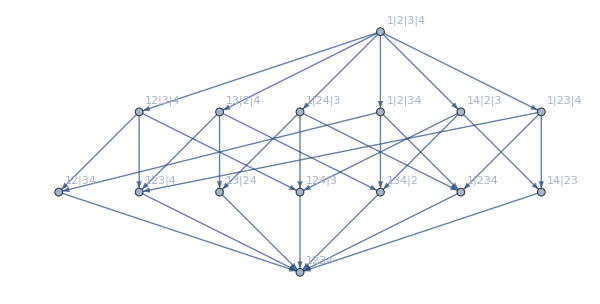

```mathematica
g=Graph[MobiusGraphSimple[K4Key,allGraphs4]]
```

```mathematica
DoubleVertices=Select[VertexList[g],StringCount[SymbolName[#],"x"]==2&]
```

{n12x3x4,n13x2x4,n14x2x3,n1x23x4,n1x24x3,n1x2x34}

```mathematica
TableForm[
Sort[
Tally[
Table[
PartitionIntersect[set],
{set, Subsets[DoubleVertices,{1,6}]}
]
]
],TableDepth->1
]
```

{{1,3,1},6}
{{2,5,1},15}
{{3,6,1},16}
{{3,7,1},4}
{{4,6,1},3}
{{4,7,1},12}
{{5,7,1},6}
{{6,7,1},1}

```mathematica
g=Graph[MobiusGraphSimple[K6Key,allGraphs6]];
```

```mathematica
DoubleVertices=Select[VertexList[g],StringCount[SymbolName[#],"x"]==4&];Length[DoubleVertices]
```

15

```mathematica
TableForm[
Sort[
Tally[
Monitor[
Table[
PartitionIntersect[set],
{set, Subsets[DoubleVertices,{1,15}]}
],
set]
]
],TableDepth->1
]
```

{{1,10,25,15,1},15}
{{2,19,44,23,1},105}
{{3,27,58,27,1},435}
{{3,28,63,31,1},20}
{{4,34,67,27,1},45}
{{4,34,68,29,1},1080}
{{4,35,72,31,1},240}
{{5,40,74,29,1},405}
{{5,40,75,30,1},1296}
{{5,40,75,31,1},72}
{{5,41,78,31,1},1140}
{{5,42,81,31,1},90}
{{6,45,77,29,1},60}
{{6,45,79,30,1},1080}
{{6,45,80,30,1},60}
{{6,45,80,31,1},360}
{{6,46,81,31,1},360}
{{6,46,82,31,1},2160}
{{6,47,84,31,1},910}
{{6,49,90,31,1},15}
{{7,49,81,30,1},300}
{{7,49,82,30,1},180}
{{7,49,83,31,1},180}
{{7,50,84,31,1},1980}
{{7,50,85,31,1},360}
{{7,51,84,31,1},180}
{{7,51,86,31,1},2700}
{{7,52,87,31,1},420}
{{7,53,90,31,1},135}
{{8,52,82,30,1},15}
{{8,52,83,30,1},90}
{{8,53,85,31,1},360}
{{8,53,86,31,1},360}
{{8,54,86,31,1},900}
{{8,54,87,31,1},1440}
{{8,54,88,31,1},180}
{{8,55,88,31,1},2460}
{{8,56,87,31,1},90}
{{8,56,90,31,1},360}
{{8,57,90,31,1},180}
{{9,54,84,30,1},10}
{{9,56,86,31,1},90}
{{9,56,87,31,1},360}
{{9,56,88,31,1},60}
{{9,57,88,31,1},1260}
{{9,57,89,31,1},360}
{{9,58,88,31,1},450}
{{9,58,89,31,1},1215}
{{9,58,90,31,1},180}
{{9,59,90,31,1},960}
{{9,61,90,31,1},60}
{{10,58,88,31,1},60}
{{10,59,88,31,1},225}
{{10,59,89,31,1},360}
{{10,60,89,31,1},720}
{{10,60,90,31,1},432}
{{10,61,90,31,1},900}
{{10,62,90,31,1},300}
{{10,65,90,31,1},6}
{{11,61,89,31,1},240}
{{11,61,90,31,1},90}
{{11,62,90,31,1},420}
{{11,63,90,31,1},585}
{{11,65,90,31,1},30}
{{12,62,89,31,1},15}
{{12,63,90,31,1},180}
{{12,64,90,31,1},200}
{{12,65,90,31,1},60}
{{13,64,90,31,1},45}
{{13,65,90,31,1},60}
{{14,65,90,31,1},15}
{{15,65,90,31,1},1}

```mathematica
Select[Subsets[DoubleVertices,{3}],PartitionIntersect[#]=={3,28,63,31,1}&]
```

{}

```mathematica
TableForm[
Sort[
Tally[
Monitor[
Table[
PartitionIntersect[set],
{set, Subsets[DoubleVertices,{3}]}
],
set]
]
],TableDepth->1
]
```

```mathematica
g=Graph[MobiusGraphSimple[K3Key,allGraphs3]];
```

```mathematica
DoubleVertices=Select[VertexList[g],StringCount[SymbolName[#],"x"]==1&];Length[DoubleVertices]
```

3

```mathematica
TableForm[
Sort[
Tally[
Monitor[
Table[
PartitionIntersect[set],
{set, Subsets[DoubleVertices,{1,3}]}
],
set]
]
],TableDepth->1
]
```

{{1,1},3}
{{2,1},3}
{{3,1},1}

```mathematica
g=Graph[MobiusGraphSimple[1,allGraphs2]];
```

```mathematica
DoubleVertices=Select[VertexList[g],StringCount[SymbolName[#],"x"]==0&];Length[DoubleVertices]
```

1

```mathematica
TableForm[
Sort[
Tally[
Monitor[
Table[
PartitionIntersect[set],
{set, Subsets[DoubleVertices,{1,3}]}
],
set]
]
],TableDepth->1
]
```

{{},1}